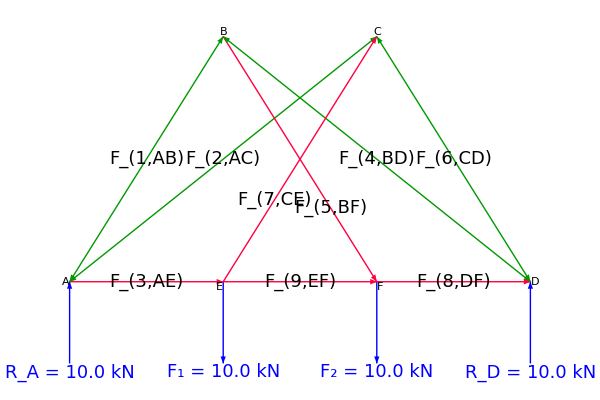

```mathematica
Module[{FA,FB,w,h,sol,RA,RB,colC,colT,scale},
FA=10;FB=10;w=5;h=5;

sol=Quiet@Solve[N@{w*FA+2*w*FB-3*w*rb==0,ra+rb-FA-FB==0},{ra,rb}][[1]];
RA=ra/.sol;RB=rb/.sol;

colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];
scale[F_]:=Rescale[F,{0,15}];

Graphics[{Thick,
{Blue,
Arrow[{{w,0},{w,-h/2*scale[FA]}}],Arrow[{{2*w,0},{2*w,-h/2*scale[FB]}}],
If[#2≠0,Text[Style[Row@{Subscript[Style["F",Italic],#1]," = ",NumberForm[#2,{3,1}]," kN"},18],{#3,-h/2*scale[#2]},{0,1.2}]]&@@@{{"1",FA,w},{"2",FB,2*w}},
Arrow[{{0,-h/2*scale[RA]},{0,0}}],Arrow[{{3*w,-h/2*scale[RB]},{3*w,0}}],
If[#2≠0,Text[Style[Row@{Subscript[Style["R",Italic],#1]," = ",NumberForm[N@#2,{3,1}]," kN"},18],{#3,-h/2*scale[#2]},{0,1.2}]]&@@@{{"A",RA,0},{"D",RB,3*w}}},

{colC,Arrowheads@{-0.04,0.04},Arrow[{{0,0},{w,h}}],Arrow[{{w,h},{3*w,0}}],Arrow[{{2*w,h},{0,0}}],Arrow[{{2*w,h},{3*w,0}}]},

{colT,Arrowheads@{{0.045,0.4},{-0.045,0.6}},Arrow[{{0,0},{w,0}}],Arrow[{{w,0},{2*w,0}}],Arrow[{{2*w,0},{3*w,0}}],Arrow[{{w,0},{2*w,h}}],Arrow[{{w,h},{2*w,0}}]},

Text[Framed[Style[Row@{" ",#1," "},16],RoundingRadius->15],#2,#3]&@@@{
{"A",{0,0},{1,0}},{"B",{w,h},{0,-1}},{"C",{2*w,h},{0,-1}},{"D",{3*w,0},{-1,0}},{"E",{w,0},{1,1.2}},{"F",{2*w,0},{-1,1.2}}},

Text[Style[Subscript[Style["F",Italic],#1],18,Background->White],#2]&@@@{
{"1,AB",{w/2,h/2}},{"5,BF",{w+0.7*w,0.3*h}},{"3,AE",{w/2,0}},{"7,CE",{w+w/3,h/3}},{"6,CD",{2*w+w/2,h/2}},{"8,DF",{2*w+w/2,0}},{"9,EF",{w+w/2,0}},{"4,BD",{(w+3*w)/2,h/2}},{"2,AC",{w,h/2}}},
},ImageSize->{600,400}]
]
```

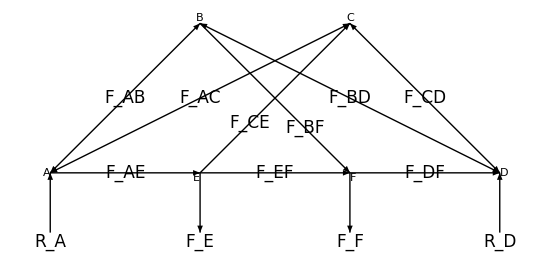

```mathematica
Module[{FA,FB,w,h,δ},
FA=10;FB=10;w=5;h=5;δ=2;

Graphics[{Thick,
{Arrow[{{w,0},{w,-δ}}],Arrow[{{2*w,0},{2*w,-δ}}],
If[#2≠0,Text[Style[Subscript[Style["F",Italic],#1],17],{#2,-δ},{0,1.2}]]&@@@{{"E",w},{"F",2*w}},
Arrow[{{0,-δ},{0,0}}],Arrow[{{3*w,-δ},{3*w,0}}],
Text[Style[Subscript[Style["R",Italic],#1],17],{#2,-δ},{0,1.2}]&@@@{{"A",0},{"D",3*w}}},

{Arrowheads@{-0.035,0.035},Arrow[{{0,0},{w,h}}],Arrow[{{w,h},{3*w,0}}],Arrow[{{2*w,h},{0,0}}],Arrow[{{2*w,h},{3*w,0}}]},

{Arrowheads@{{0.035,0.4},{-0.035,0.6}},Arrow[{{0,0},{w,0}}],Arrow[{{w,0},{2*w,0}}],Arrow[{{2*w,0},{3*w,0}}]},

{Arrowheads@{{0.035,0.25},{-0.035,0.375}},Arrow[{{w,0},{2*w,h}}]},
{Arrowheads@{{0.035,0.625},{-0.035,0.75}},Arrow[{{w,h},{2*w,0}}]},

Text[Framed[Style[Row@{" ",#1," "},16],RoundingRadius->15,FrameMargins->Small],#2,#3]&@@@{
{"A",{0,0},{1,0}},{"B",{w,h},{0,-1}},{"C",{2*w,h},{0,-1}},{"D",{3*w,0},{-1,0}},{"E",{w,0},{1,1.2}},{"F",{2*w,0},{-1,1.2}}},

Text[Style[Subscript[Style["F",Italic],#1],17,Background->White],#2]&@@@{
{"AB",{w/2,h/2}},{"BF",{w+0.7*w,0.3*h}},{"AE",{w/2,0}},{"CE",{w+w/3,h/3}},{"CD",{2*w+w/2,h/2}},{"DF",{2*w+w/2,0}},{"EF",{w+w/2,0}},{"BD",{(w+3*w)/2,h/2}},{"AC",{w,h/2}}},
},ImageSize->550]
]
```

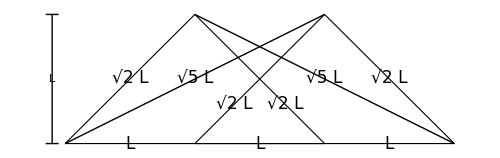

```mathematica
Module[{FA,FB,w,h,δ},
FA=10;FB=10;w=5;h=5;δ=2;

Graphics[{Thick,
(*{Arrow[{{w,0},{w,-δ}}],Arrow[{{2*w,0},{2*w,-δ}}],
If[#2≠0,Text[Style[Subscript[Style["F",Italic],#1],17],{#2,-δ},{0,1.2}]]&@@@{{"E",w},{"F",2*w}},
Arrow[{{0,-δ},{0,0}}],Arrow[{{3*w,-δ},{3*w,0}}],
Text[Style[Subscript[Style["R",Italic],#1],17],{#2,-δ},{0,1.2}]&@@@{{"A",0},{"D",3*w}}},*)

(*{Arrowheads@{-0.035,0.035},Arrow[{{0,0},{w,h}}],Arrow[{{w,h},{3*w,0}}],Arrow[{{2*w,h},{0,0}}],Arrow[{{2*w,h},{3*w,0}}]},

{Arrowheads@{{0.035,0.4},{-0.035,0.6}},Arrow[{{0,0},{w,0}}],Arrow[{{w,0},{2*w,0}}],Arrow[{{2*w,0},{3*w,0}}]},

{Arrowheads@{{0.035,0.25},{-0.035,0.375}},Arrow[{{w,0},{2*w,h}}]},
{Arrowheads@{{0.035,0.625},{-0.035,0.75}},Arrow[{{w,h},{2*w,0}}]},*)
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,0},{2*w,0},{w,h}}],Polygon[{{3*w,0},{w,0},{2*w,h}}]},
Line[{{w,h},{3*w,0}}],Line[{{2*w,h},{0,0}}],

(*Text[Framed[Style[Row@{" ",#1," "},16],RoundingRadius->15,FrameMargins->Small],#2,#3]&@@@{
{"A",{0,0},{1,0}},{"B",{w,h},{0,-1}},{"C",{2*w,h},{0,-1}},{"D",{3*w,0},{-1,0}},{"E",{w,0},{1,1.2}},{"F",{2*w,0},{-1,1.2}}},*)

Text[Style[Row@{#1,Style[" L",Italic]},17,Background->White],#2]&@@@{{√2,{w/2,h/2}},{√2,{w+0.7*w,0.3*h}},{"",{w/2,0}},{√2,{w+0.3*w,0.3*h}},{√2,{2*w+w/2,h/2}},{"",{2*w+w/2,0}},{"",{w+w/2,0}},{√5,{(w+3*w)/2,h/2}},{√5,{w,h/2}}},

{Thin,Line[{{-0.5,0},{-0.5,h}}],Line[{{-0.75,#},{-0.25,#}}]&/@{0,h}},
Text[Framed[Style["L",Italic,17],Background->White,FrameStyle->None,FrameMargins->Tiny],{-0.5,0.5*h}]
},ImageSize->500]
]
```